```mathematica
(* Everything in SI units *)
L = 1; (* Length of string *)
T = 65.0; (* Tension in string *)
μ = 0.005; (* Linear mass density *)
Y = 2.0*10^11; (* Young's modulus *)
r = 0.000254; (* Radius of string *)
A = π r^2;  (* Cross-sectional area *)
k = r/2(* Radius of gyration *) ;
```

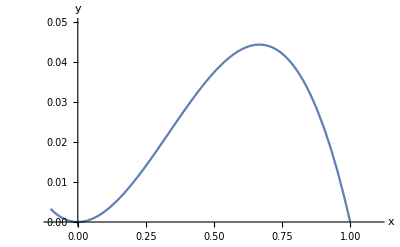

```mathematica
amp = 0.05; (* Initial max displacement (amplitude) *)
mid = L/2; (* For triangular y0 -- the distance from the left end at which the initial peak lies *)
lend = 0; (* Left end of triangle wave *)
rend = L; (* Right end of triangle wave *)
y0 = Piecewise[{{0, x<lend || x>rend},{amp/(mid-lend)(x-lend), x<=mid}, {-amp/(rend-mid)(x-rend), x>=mid}}]; (* y0: Example initial condition for y[x,t] -- triangular 'pluck' *)
y0f = amp Sin[(π x)/L]; (* y0f: Initial condition for y[x,t] matching profile of fundamental (n=1) analytical solution *)
y0test = 6amp*x^2*(L-x); (* y0test : Test initial condition *);
Plot[6amp*x^2*(L-x), {x, -L/10, L+L/10}, PlotRange->{{-L/10, L+L/10},{0, amp}}, AxesLabel->{"x", "y"}] (* Plotting initial condition y0test *)
```

```mathematica
eqn = μ D[y[x,t], {t, 2}] - T D[y[x,t], {x, 2}] + Y A k^2 D[y[x,t], {x,4}]; (* The full differential equation (== 0) in terms of y *)
eqn2 = μ D[y[x,t], {t, 2}] - T a[x,t] + Y A k^2 D[a[x,t], {x,2}]; (* For NDSolve requirements, we redefine eqn so we do not exceed second order spatial derivatives. a := Subscript[y, xx] *)
```

```mathematica
(* Computing analytical fundamental frequencies for comparison with numerical solutions *)
β = (π^2 Y A k^2)/(T L^2);
v = Sqrt[T/μ];
ff0 = v/(2 L);
period1 = 1/(ff0 Sqrt[1 + β]) (* Analytical fundamental (n=1) period *)
```

0.0175403

```mathematica
sol2 = NDSolve[{eqn2==NeumannValue[0, t==0],
Derivative[2,0][y][x,t] == a[x,t],
DirichletCondition[y[x,t] == 0, x<=0 || x>=L],
DirichletCondition[a[x,t] == 0, x<=0 || x>=L],
y[x,0] == y0test}, (* Initial conditions *)
 {y[x,t], a[x,t]}, {x, 0, L}, {t, 0, 0.035},
MaxStepSize->10^-100,
AccuracyGoal->Infinity,(* These three options didn't seem to change the runtime, so probably negligible compared to default *)
InterpolationOrder->All,
MaxSteps->Infinity,
PrecisionGoal->100,
StartingStepSize->10^-10,
Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->10^-6}}}]
```

{{y[x,t]→InterpolatingFunction[{{0., 1.}, {0., 0.035}}, <>][x,t],a[x,t]→InterpolatingFunction[{{0., 1.}, {0., 0.035}}, <>][x,t]}}

```mathematica
(* Generating animation of string evolution over time; code adapted from https://community.wolfram.com/groups/-/m/t/140338 *)
Animate[Grid[{{"t=",i," seconds"},{Plot[Evaluate[y[x,t]/. sol2/. t->i],{x, -L/10, L+L/10},AxesLabel->{"x","y(x,t)"}, PlotRange->{{0,L},{-amp,amp}},ImageSize->300,PlotStyle->Red],SpanFromLeft}}],{i,0,0.035,.00001}, AnimationRunning->False] 
(* See the {i, Subscript[t, initial], Subscript[t, final], Δt} argument to modify animation start/stop/framerate *)
```